```mathematica
SetDirectory[NotebookDirectory[]];
Import["Modules/Welcome.m"];
Import["Modules/File_manager.m"];
Import["Modules/SlideMenuManager.m"];
Import["Modules/Options.m"];
ClearUserSession[];
ModuleDirectoryMenu["_intro"];
CellPrint[TextCell["","",CellTags->{"_intro"}]];
ModuleOptions[];
ModuleWelcome [];
```

Homepage | Menu Utente | Bibliografia | Chi siamo?

| -Graphics-

| -Graphics- | -Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];

Import["Modules/SlideMenuManager.m"];
ModuleDirectoryMenu["_user"];
CellPrint[TextCell["","",CellTags->{"_user"}]];

Import["Modules/File_manager.m"];
Import["Modules/User_login.m"];

Init[ NotebookDirectory[] ];
GetUserLoginGraphicInterface[];
```

Homepage | Menu Utente | Bibliografia | Chi siamo?

Registrazione

Inserisci il tuo nome nel campo seguente per salvare i tuoi progressi

Login

```mathematica
Import["Modules/SlideMenuManager.m"];
ModuleDirectoryMenu["_bibliografia"];
CellPrint[TextCell["","",CellTags->{"_bibliografia"}]];
Import["Modules/Biblio.m"];
ModuleBiblio[];
```

Homepage | Menu Utente | Bibliografia | Chi siamo?

Import::nffil: File not found during Import.

```mathematica
Import["Modules/SlideMenuManager.m"];
ModuleDirectoryMenu["_about"];
CellPrint[TextCell["","",CellTags->{"_about"}]];
Import["Modules/About.m"];
ModuleAbout[];
```

Homepage | Menu Utente | Bibliografia | Chi siamo?

| -Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
CellPrint[TextCell["","",CellTags->{"_help"}]];
Import["Modules/Hep.m"];
ModuleHelp[];
```

Import::nffil: File not found during Import.

Teorema di Euclide

In un triangolo rettangolo il quadrato costruito su un cateto è equivalente al rettangolo che ha i lati congruenti all'ipotenusa e alla proiezione dello stesso cateto su di essa. | -Graphics-

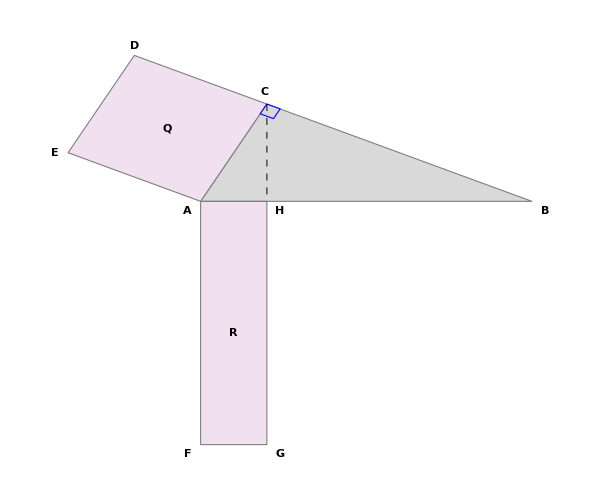
-Graphics- | -Graphics-

Non comprendi i simboli?

|  |  | Prossima Slide

```mathematica
CellPrint[TextCell["","",CellTags->{"_EuclideEnunciato"}]];
SetDirectory[NotebookDirectory[]];
Import["Modules/EuclideEnunciato.m"];
ModuleEuclideEnunciato[];
```

```mathematica
CellPrint[TextCell["","",CellTags->{"_EuclideDimostrazione"}]];
SetDirectory[NotebookDirectory[]];
Import["Modules/EuclideDimostrazione.m"];
ModuleEuclideDimostrazione [];
```

Dimostrazione del teorema di Euclide

Slide Precedente |  |  | Prossima Slide

Dimostrazione Grafica:

Teorema di Euclide - Spiegazione matematica

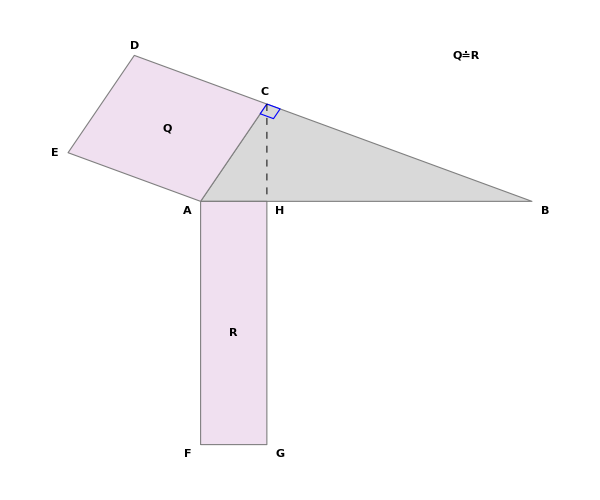

Seguendo l'enunciato del primo teorema di Euclide avremo che

AC^2 = AH x AB

AC^2 rappresenta l'area del quadrato costruito sul cateto AC, mentre AH x AB è l'area del rettangolo che ha per dimensioni la proiezione
del cateto AC sull'ipotenusa e l'ipotenusa stessa

Alla luce di questo possiamo affermare che: in un triangolo rettangolo, ciascun cateto è il medio proporzionaletra l'ipotenusa e la proiezione
del cateto sull'ipotenusa

In formule questo si traduce nelle seguenti proporzioni:

AB : CB = CB : HB

AB : AC = AC : AH

Esercizio svolto:

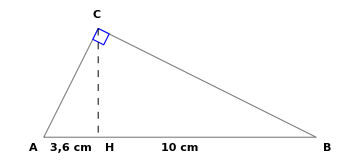

Calcolare il perimetro del triangolo rettangolo la cui ipotenusa misura 10 cm e la proiezione del cateto minore sull'ipotenusa misura 3,6 cm

Risoluzione

Conosciamo l'ipotenusa AB = 10 cm e la proiezione del cateto minore sull'ipotenusa AH = 3.6 cm. Grazie al primo teorema di Euclide 
possiamo costruire la proporzione per calcolare la lunghezza del cateto minore AC :

AB : AC = AC : AH

Sostituendo i dati avremo:

10 : AC = AC : 3,6

Utilizzando la proprietà fondamentale delle proporzioni otteniamo:

AC^2 =  10 x 3,6

AC = √36 = 6 cm

Possiamo ricavare adesso BH come differenza (AB - AH) :

BH =  10 - 3,6 = 6,4 cm

Utilizziamo infine il teorema di Euclide per determinare la lunghezza del cateto maggiore BC :

AB : BC = BC : BH

10 : BC = BC : 6,4

BC^2 =  10 x 6,4

BC = √64 = 8 cm

Infine il perimetro P è dato dalla somma della lunghezza dei lati ottenuti:

P = AB + BC + AC = 10 + 8 + 6 = 24 cm

Slide Precedente |  |  | Prossima Slide

```mathematica
CellPrint[TextCell["","",CellTags->{"_EuclideEsempi"}]];
SetDirectory[NotebookDirectory[]];
Import["Modules/EuclideEsempi.m"];
ModuleEuclideEsempi [];
```

## Euclide: Esercizi

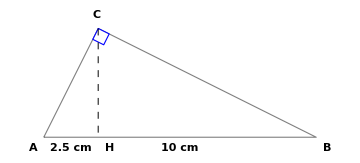

Calcolare la lunghezza del lato AC del triangolo rettangolo la cui ipotenusa misura 10 cm e la proiezione del cateto minore sull'ipotenusa misura 2.5 cm

Nel caso di risultato con cifre decimali, arrotondare alla prima cifra

Verifica

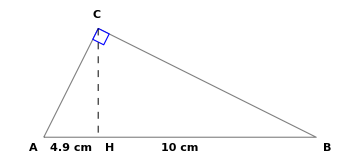

Calcolare il perimetro del triangolo rettangolo la cui ipotenusa misura 10 cm e la proiezione del cateto minore sull'ipotenusa misura 4.9 cm

Nel caso di risultato con cifre decimali, arrotondare alla seconda cifra

Verifica

Slide Precedente |  |  | Torna alla Home

```mathematica
CellPrint[TextCell["","",CellTags->{"_EuclideEsercizi"}]];
SetDirectory[NotebookDirectory[]];
Import["Modules/EuclideEsercizi.m"];
ModuleEuclideEsercizi [];
```

Teorema di Pitagora

In un triangolo rettangolo il quadrato costruito sull'ipotenusa è equivalente alla somma dei quadrati costruiti sui cateti. | -Graphics-

AB^2+BC^2=AC^2

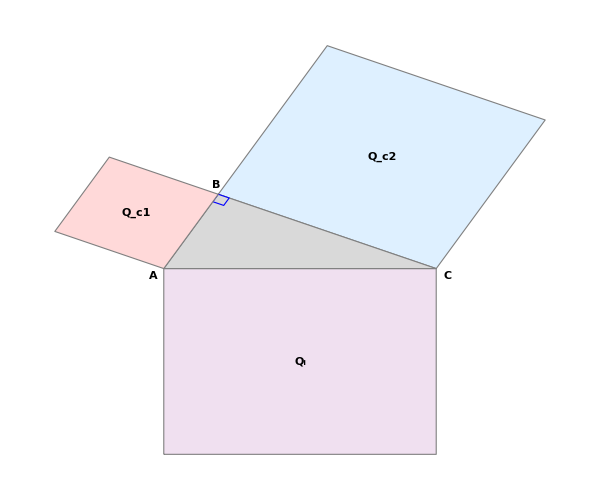
-Graphics- | -Graphics-

|  |  | Prossima Slide

```mathematica
CellPrint[TextCell["","",CellTags->{"_PitagoraEnunciato"}]];
SetDirectory[NotebookDirectory[]];
Import["Modules/PitagoraEnunciato.m"];
ModulePitagoraEnunciato [];
```

```mathematica
CellPrint[TextCell["","",CellTags->{"_PitagoraDimostrazione"}]];
SetDirectory[NotebookDirectory[]];
Import["Modules/PitagoraDimostrazione.m"];
ModulePitagoraDimostrazione [];
```

Dimostrazione del teorema di Pitagora

Slide Precedente |  |  | Prossima Slide

Dimostrazione Grafica:

Formule del teorema di Pitagora:

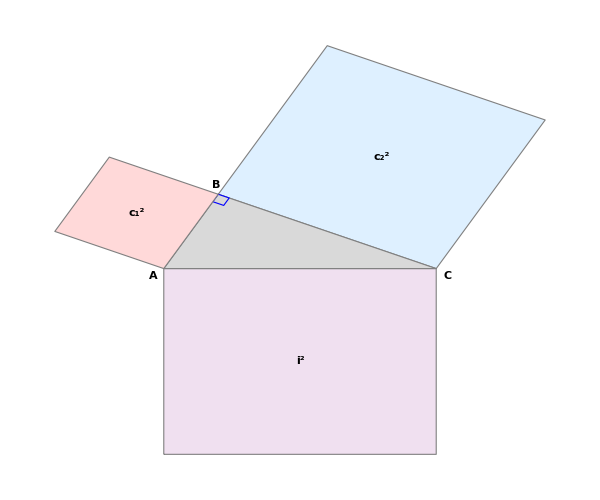

Seguendo l'enunciato del teorena di pitagora (indicando con 'c_1' e 'c_2' i cateti e con 'i' l'ipotenusa)

i^2 = c_1^2+c_2^2

possiamo ricavare le seguenti uguaglianze

c_1^2 = i^2-c_2^2

c_2^2 = i^2-c_1^2

E da questi, a loro volta possiamo ricavare le seguenti formule per il calcolo delle misure dei lati, applicando la radice quadrata

i = √(c_1^2+c_2^2)

c_1 = √(i_^2-c_2^2)

c_2 = √(i_^2-c_1^2)

Esercizio svolto:

Di un Rettangolo ABC retto in B, conosciamo la lunghezza dell'ipotenusa AC e del cateto BC rispettivamente AC=5 cm e AB=3 cm.

Vogliamo trovare la lunghezza del cateto CB

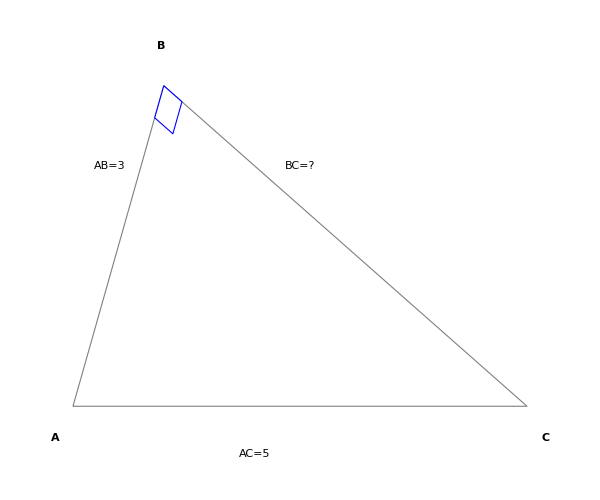

Svolgimento:

Dalle formule relative al teorema di Pitagora sappiamo che, data la lunghezza di un cateto e quella dell'ipotenusa è possibile ricavare la lunghezza del cateto rimasto:

Cateto = √(Ipotenusa_^2 - (Altro Cateto)_^2)

Ottenuamo così

CB = √(AC_^2 - BC_^2) = √(5_^2 - 3_^2) = √(25 - 9) = √16 = 4

Applicazione pratica delle formule del teorema: Distanza tra punti in un piano

Con distanza tra due punti nel piano cartesiano (o distanza euclidea) ci si riferisce alla formula che permette di calcolare la distanza tra due punti a partire dalle coordinate cartesiane.

tale distanza è per definizione non negativa, dunque è positiva oppure è nulla nel caso in cui i due punti coincidano.

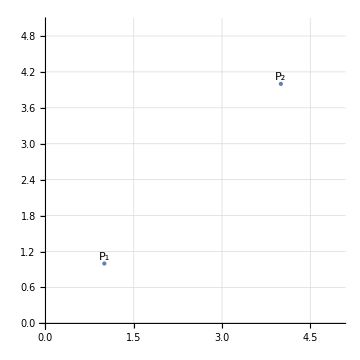

Dati due punti nel piano cartesiano caratterizzati ciscuno da una coppia di coordinate cartesiane (ascissa,ordinata)

Per calcolare la distanza euclidea tra due puntiP_1 P_2 indicandola con d(P_1 P_2)

Possiamo costruire un triangolo rettangolo in cui il segmento cercato P_1P_2 è l'ipotenusa, ed utilizzare quindi il teorema di Pitagora.

Essendo i due cateti paralleli agli assi, sappiamo calcolarne facilmente la lunghezza.

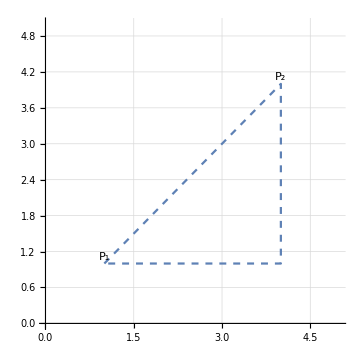

La formula finale è piuttosto semplice: si applica il teorema di Pitagora, dove un cateto si ottiene come differenza delle ascisse dei due punti e l'altro sottraendo le loro ordinate.

d(P_1 P_2) = √(((X)_P_1-X_P_2)^2 + ((Y)_P_1-Y_P_2)^2)

Terne Pitagoriche

Una terna pitagorica è una terna di numeri interi a, b, c tali che soddisfino la condizione:

a^2 + b^2= c^2

Ad esempio (3, 4, 5) è una terna pitagorica, mentre (1, 1, √2) non è una terna pitagorica in quanto l'ultimo numero (c) non è intero

Nell'animazione è possibile dimostrare graficamente che:  3^2 + 4^2= 5^2

Terne Pitagoriche Primitive e Derivate

Una terna come (3, 4, 5) è detta primitiva mentre una terna come (6, 8, 10) è detta derivata. Ne consegue che una terna pitagorica si definisce
'primitiva' quando i termini a e b sono coprimi

Data la terna pitagorica primitiva (a, b, c) si definisce una terna pitagorica derivata la terna:

(ka, kb, kc) con k numero intero positivo

Slide Precedente |  |  | Prossima Slide

```mathematica
CellPrint[TextCell["","",CellTags->{"_PitagoraEsempi"}]];
SetDirectory[NotebookDirectory[]];
Import["Modules/PitagoraEsempi.m"];
ModulePitagoraEsempi [];
```

| -Graphics-
 |        Clicca per iniziare gli esercizi!

Slide Precedente |  |  | Torna alla Home

Data la triade pitagorica a,b,c determinare b sapendo che a = 7 e c = 25

Nel caso di risultato con cifre decimali, arrotondare alla prima cifra

Verifica

Data la triade pitagorica a,b,c determinare b sapendo che a = 56 e c = 106

Nel caso di risultato con cifre decimali, arrotondare alla prima cifra

Verifica

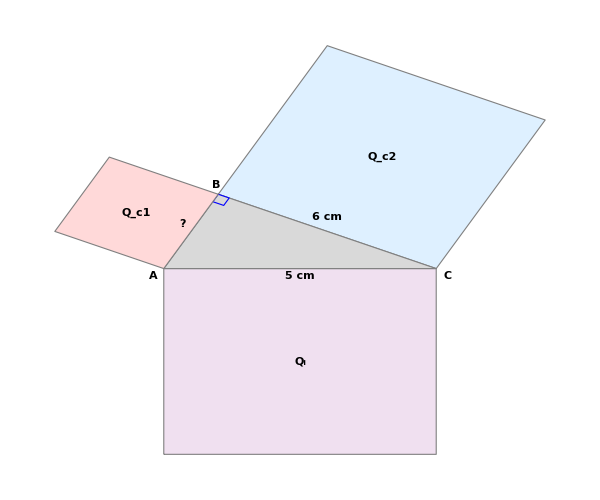

Dato il triangolo ABC, calcolare la lunghezza del cateto AB e l'area del quadrato Q_c1 sapendo che il lato AC è lungo 5cm e il lato BC è lungo 6cm

Nel caso di risultato con cifre decimali, arrotondare alla prima cifra

Verifica

Suggerimento?

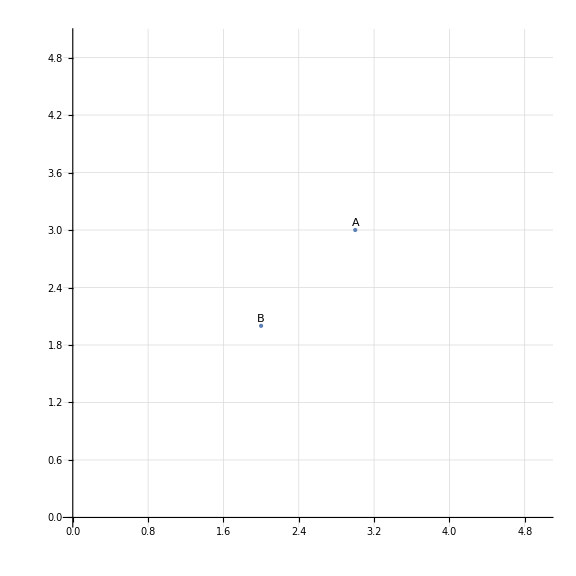

Calcola la distanza tra i due punti A e B sul piano cartesiano

Nel caso di risultato con cifre decimali, arrotondare alla prima cifra

Verifica

```mathematica
CellPrint[TextCell["","",CellTags->{"_PitagoraEsercizi"}]];
SetDirectory[NotebookDirectory[]];
Import["Modules/PitagoraEsercizi.m"];
ModulePitagoraEsercizi [];
```